```mathematica
ϕ[x_] :=1
```

```mathematica
θ[y_] := y
```

```mathematica
ϕ[x_, y_] := ArcSin[Sin[x]/Cos[θ[y]]
```

```mathematica
D[ϕ[x], x]
```

(Cos[x] Sec[θ])/(√(1-Sec[θ]^2 Sin[x]^2))

```mathematica
D[ϕ[x], θ]
```

(Sec[θ] Sin[x] Tan[θ])/(√(1-Sec[θ]^2 Sin[x]^2))

```mathematica
D[θ[y], y]
```

1

```mathematica
D[θ[y], x]
```

0

```mathematica
D[D[θ[y], y], y]
```

0

```mathematica
D[D[θ[y], y], x]
```

0

```mathematica
D[D[θ[y], x], x]
```

0

```mathematica
D[D[θ[y], x], y]
```

0

```mathematica
D[ϕ[{x, y}], x]
```

{(Cos[x] Sec[θ])/(√(1-Sec[θ]^2 Sin[x]^2)),0}

```mathematica
ϕ[]
```

{0,0}

```mathematica
ϕ[x_, y_] := ArcSin[Sin[x]/Cos[θ[y]]]
```

```mathematica
D[ϕ[x, y], x]
```

(Cos[x] Sec[y])/(√(1-Sec[y]^2 Sin[x]^2))

```mathematica
D[ϕ[x, y], y]
```

(Sec[y] Sin[x] Tan[y])/(√(1-Sec[y]^2 Sin[x]^2))

```mathematica
D[D[ϕ[x, y], x], x]
```

(Cos[x]^2 Sec[y]^3 Sin[x])/((1-Sec[y]^2 Sin[x]^2)^(3/2))-(Sec[y] Sin[x])/(√(1-Sec[y]^2 Sin[x]^2))

```mathematica
D[D[ϕ[x, y], x], y]
```

(Cos[x] Sec[y]^3 Sin[x]^2 Tan[y])/((1-Sec[y]^2 Sin[x]^2)^(3/2))+(Cos[x] Sec[y] Tan[y])/(√(1-Sec[y]^2 Sin[x]^2))

```mathematica
D[D[ϕ[x, y], y], y]
```

(Sec[y]^3 Sin[x])/(√(1-Sec[y]^2 Sin[x]^2))+(Sec[y]^3 Sin[x]^3 Tan[y]^2)/((1-Sec[y]^2 Sin[x]^2)^(3/2))+(Sec[y] Sin[x] Tan[y]^2)/(√(1-Sec[y]^2 Sin[x]^2))

```mathematica
D[D[ϕ[x, y], y], x]
```

(Cos[x] Sec[y]^3 Sin[x]^2 Tan[y])/((1-Sec[y]^2 Sin[x]^2)^(3/2))+(Cos[x] Sec[y] Tan[y])/(√(1-Sec[y]^2 Sin[x]^2))

```mathematica
D[D[ϕ[x, y], y], x] == D[D[ϕ[x, y], x], y]
```

True

```mathematica
FullSimplify[D[D[ϕ[x, y], x], x]]
```

(Sec[y] Sin[x] Tan[y]^2)/((1-Sec[y]^2 Sin[x]^2)^(3/2))

```mathematica
FullSimplify[D[D[ϕ[x, y], x], y]]
```

(Cos[x] Sec[y] Tan[y])/((1-Sec[y]^2 Sin[x]^2)^(3/2))

```mathematica
FullSimplify[D[D[ϕ[x, y], y], x]]
```

(Cos[x] Sec[y] Tan[y])/((1-Sec[y]^2 Sin[x]^2)^(3/2))

```mathematica
FullSimplify[D[D[ϕ[x, y], y], y]]
```

-(Sec[y] Sin[x] (-Sec[y]^2+Sec[y]^4 Sin[x]^2-Tan[y]^2))/((1-Sec[y]^2 Sin[x]^2)^(3/2))

```mathematica
xxx = FullSimplify[D[D[D[ϕ[x, y], x], x],x]]
```

(Cos[x] (3-2 Cos[2 x]+Cos[2 y]) Sec[y]^3 Tan[y]^2)/(2 (1-Sec[y]^2 Sin[x]^2)^(5/2))

```mathematica
xxy = FullSimplify[D[D[D[ϕ[x, y], x], x],y]]
```

-((-3-2 Cos[2 x]+Cos[2 y]) Sec[y]^3 Sin[x] Tan[y])/(2 (1-Sec[y]^2 Sin[x]^2)^(5/2))

```mathematica
xyx = FullSimplify[D[D[D[ϕ[x, y], x], y],x]]
```

-((-3-2 Cos[2 x]+Cos[2 y]) Sec[y]^3 Sin[x] Tan[y])/(2 (1-Sec[y]^2 Sin[x]^2)^(5/2))

```mathematica
xyy = FullSimplify[D[D[D[ϕ[x, y], x], y],y]]
```

(Cos[x] (5+4 Cos[2 x] Cos[2 y]-Cos[4 y]) Sec[y]^5)/(8 (1-Sec[y]^2 Sin[x]^2)^(5/2))

```mathematica
yxx = FullSimplify[D[D[D[ϕ[x, y], y], x],x]]
```

-((-3-2 Cos[2 x]+Cos[2 y]) Sec[y]^3 Sin[x] Tan[y])/(2 (1-Sec[y]^2 Sin[x]^2)^(5/2))

```mathematica
yxy = FullSimplify[D[D[D[ϕ[x, y], y], x],y]]
```

(Cos[x] (5+4 Cos[2 x] Cos[2 y]-Cos[4 y]) Sec[y]^5)/(8 (1-Sec[y]^2 Sin[x]^2)^(5/2))

```mathematica
yyx =FullSimplify[D[D[D[ϕ[x, y], y], y],x]]
```

(Cos[x] (5+4 Cos[2 x] Cos[2 y]-Cos[4 y]) Sec[y]^5)/(8 (1-Sec[y]^2 Sin[x]^2)^(5/2))

```mathematica
yyy = FullSimplify[D[D[D[ϕ[x, y], y], y],y]]
```

(Sec[y] Sin[x] (-1+(5+Cos[2 x]) Sec[y]^2-5 Sec[y]^4 Sin[x]^2+2 Sec[y]^6 Sin[x]^4) Tan[y])/((1-Sec[y]^2 Sin[x]^2)^(5/2))

```mathematica
xxy == xyx == yxx
```

True

```mathematica
xyy == yyx == yxy
```

True

```mathematica
Θ0 := 0.5*Pi
```

```mathematica
θ[x_, y_,  Θ0_ ] := ArcSin[Sin[Θ0 + y] Cos[x]]
```

```mathematica
FullSimplify[θ[0, 0]]
```

ArcSin[Sin[ϕ]]

```mathematica
ArcSin[Sin[0]] == Θ
```

ArcSin[Sin[Θ]]==Θ

```mathematica
D[θ[x, y],x]
```

-(Sin[x] Sin[y+Θ])/(√(1-Cos[x]^2 Sin[y+Θ]^2))

```mathematica
D[θ[x, y],y]
```

(Cos[x] Cos[y+Θ])/(√(1-Cos[x]^2 Sin[y+Θ]^2))

```mathematica
D[D[θ[x, y],x], x]
```

(Cos[x] Sin[x]^2 Sin[y+Θ]^3)/((1-Cos[x]^2 Sin[y+Θ]^2)^(3/2))-(Cos[x] Sin[y+Θ])/(√(1-Cos[x]^2 Sin[y+Θ]^2))

```mathematica
D[D[θ[x, y],x], y]
```

-(Cos[x]^2 Cos[y+Θ] Sin[x] Sin[y+Θ]^2)/((1-Cos[x]^2 Sin[y+Θ]^2)^(3/2))-(Cos[y+Θ] Sin[x])/(√(1-Cos[x]^2 Sin[y+Θ]^2))

```mathematica
D[D[θ[x, y],y], x]
```

-(Cos[x]^2 Cos[y+Θ] Sin[x] Sin[y+Θ]^2)/((1-Cos[x]^2 Sin[y+Θ]^2)^(3/2))-(Cos[y+Θ] Sin[x])/(√(1-Cos[x]^2 Sin[y+Θ]^2))

```mathematica
D[D[θ[x, y],y], y]
```

(Cos[x]^3 Cos[y+Θ]^2 Sin[y+Θ])/((1-Cos[x]^2 Sin[y+Θ]^2)^(3/2))-(Cos[x] Sin[y+Θ])/(√(1-Cos[x]^2 Sin[y+Θ]^2))

```mathematica
D[D[θ[x, y],x], y] == D[D[θ[x, y],y], x]
```

True

```mathematica
y[ϕ_, θ_] := ArcSin[Sqrt[Sin[θ]^2/(Cos[ϕ]^2+ Sin[θ]^2 Sin[ϕ]^2)]]
```

```mathematica
FullSimplify[D[y[ϕ, θ], ϕ]]
```

√((Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^2)/((Cos[ϕ]^2+Sin[θ]^2 Sin[ϕ]^2)^2)) Tan[ϕ]

```mathematica
FullSimplify[D[y[ϕ, θ], θ]]
```

Csc[θ] Sec[θ] √((Cot[θ]^2 Sec[ϕ]^2)/((Csc[θ]^2+Tan[ϕ]^2)^2))

```mathematica
FullSimplify[D[D[y[ϕ, θ], ϕ], ϕ]]
```

1/4 (5+Cos[2 θ]-2 Cos[θ]^2 Cos[2 ϕ]) Sec[θ]^2 ((Cot[θ]^2 Sec[ϕ]^2)/((Csc[θ]^2+Tan[ϕ]^2)^2))^(3/2) (Csc[θ]^2+Tan[ϕ]^2)

```mathematica
FullSimplify[D[D[y[ϕ, θ], ϕ], θ]]
```

((-1+3 Cos[2 θ]+2 Cos[θ]^2 Cos[2 ϕ]) Csc[θ]^3 Sec[θ] Tan[ϕ] √((Cot[θ]^2 Sec[ϕ]^2)/((Csc[θ]^2+Tan[ϕ]^2)^2)))/(4 (Cos[ϕ]^2 Csc[θ]^2+Sin[ϕ]^2))

```mathematica
FullSimplify[D[D[y[ϕ, θ], θ], ϕ]]
```

((-1+3 Cos[2 θ]+2 Cos[θ]^2 Cos[2 ϕ]) Csc[θ]^3 Sec[θ] Tan[ϕ] √((Cot[θ]^2 Sec[ϕ]^2)/((Csc[θ]^2+Tan[ϕ]^2)^2)))/(4 (Cos[ϕ]^2 Csc[θ]^2+Sin[ϕ]^2))

```mathematica
FullSimplify[D[D[y[ϕ, θ], ϕ], ϕ]]
```

1/4 (5+Cos[2 θ]-2 Cos[θ]^2 Cos[2 ϕ]) Sec[θ]^2 ((Cot[θ]^2 Sec[ϕ]^2)/((Csc[θ]^2+Tan[ϕ]^2)^2))^(3/2) (Csc[θ]^2+Tan[ϕ]^2)

```mathematica
FullSimplify[y[ϕ, θ]]
```

ArcSin[√(1/(Cos[ϕ]^2 Csc[θ]^2+Sin[ϕ]^2))]

```mathematica
SphericalPlot3D[ArcSin[√(1/(Cos[ϕ]^2 Csc[θ]^2+Sin[ϕ]^2))],{θ,0,π},{ϕ,0,2 π}]
```

-Graphics3D-

```mathematica
x[ϕ_, θ_] := ArcCos[ Sin[θ]/(Sqrt[Sin[θ]^2/(Cos[ϕ]^2+ Sin[θ]^2 Sin[ϕ]^2)])]
```

```mathematica
FullSimplify[x[ϕ, θ]]
```

ArcCos[Sin[θ]/(√(1/(Cos[ϕ]^2 Csc[θ]^2+Sin[ϕ]^2)))]

```mathematica
SphericalPlot3D[ArcCos[Sin[θ]/(√(1/(Cos[ϕ]^2 Csc[θ]^2+Sin[ϕ]^2)))],{θ,0,π},{ϕ,0,2 π}]
```

-Graphics3D-

```mathematica
SphericalPlot3D[x[ϕ,θ]^2 + y[ϕ,θ]^2,{θ,0,π},{ϕ,0,2 π}]
```

-Graphics3D-

```mathematica
xx[ϕ_, θ_]  := FullSimplify[D[x[ϕ, θ], ϕ]]
```

SetDelayed::write: Tag Times in (Cot[ϕ] Csc[θ] √(Cos[θ]^2 Sin[ϕ]^2) √(1/(Cos[ϕ]^2 Csc[θ]^2+Sin[ϕ]^2)))[ϕ_,θ_] is Protected.

$Failed

```mathematica
FullSimplify[D[x[ϕ, θ], θ]]
```

-Sec[θ] √(Cos[θ]^2 Sin[ϕ]^2) √(1/(Cos[ϕ]^2 Csc[θ]^2+Sin[ϕ]^2))

```mathematica
FullSimplify[D[D[x[ϕ, θ], ϕ], ϕ]]
```

-Csc[θ] √(Cos[θ]^2 Sin[ϕ]^2) (1/(Cos[ϕ]^2 Csc[θ]^2+Sin[ϕ]^2))^(3/2)

```mathematica
FullSimplify[D[D[x[ϕ, θ], ϕ], θ]]
```

-Cot[ϕ] Csc[θ]^2 Sec[θ] √(Cos[θ]^2 Sin[ϕ]^2) (1/(Cos[ϕ]^2 Csc[θ]^2+Sin[ϕ]^2))^(3/2)

```mathematica
FullSimplify[D[D[x[ϕ, θ], θ], ϕ]]
```

-Cot[ϕ] Csc[θ]^2 Sec[θ] √(Cos[θ]^2 Sin[ϕ]^2) (1/(Cos[ϕ]^2 Csc[θ]^2+Sin[ϕ]^2))^(3/2)

```mathematica
FullSimplify[D[D[x[ϕ, θ], θ], θ]]
```

-Cos[ϕ]^2 Csc[θ]^3 √(Cos[θ]^2 Sin[ϕ]^2) (1/(Cos[ϕ]^2 Csc[θ]^2+Sin[ϕ]^2))^(3/2)

```mathematica
SphericalPlot3D[xx[ϕ, θ],{θ,0.2Pi,0.4Pi},{ϕ,0.2Pi,0.4Pi}]
```

General::ivar: 0.628319 is not a valid variable.

General::ivar: 0.628363 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics3D-

```mathematica
xx[0, 0]
```

(Cot[ϕ] Csc[θ] √(Cos[θ]^2 Sin[ϕ]^2) √(1/(Cos[ϕ]^2 Csc[θ]^2+Sin[ϕ]^2)))[0,0]

```mathematica
FullSimplify[D[x[ϕ, θ], θ]]
```

-Sec[θ] √(Cos[θ]^2 Sin[ϕ]^2) √(1/(Cos[ϕ]^2 Csc[θ]^2+Sin[ϕ]^2))

```mathematica
f[ϕ_, θ_] := -Sec[θ] √(Cos[θ]^2 Sin[ϕ]^2) √(1/(Cos[ϕ]^2 Csc[θ]^2+Sin[ϕ]^2))
```

```mathematica
FullSimplify[D[x[ϕ, θ], ϕ]]
```

Cot[ϕ] Csc[θ] √(Cos[θ]^2 Sin[ϕ]^2) √(1/(Cos[ϕ]^2 Csc[θ]^2+Sin[ϕ]^2))

0.994954

```mathematica
SphericalPlot3D[f[ϕ, θ],{θ,0,π},{ϕ,0,2 π}]
```

-Graphics3D-

```mathematica
y
```

y

```mathematica
y[ϕ_, θ_] := FullSimplify[ArcSin[Sqrt[Sin[θ]^2/(Cos[ϕ]^2+ Sin[θ]^2 Sin[ϕ]^2)]]]
```

```mathematica
FullSimplify[ArcSin[Sqrt[Sin[θ]^2/(Cos[ϕ]^2+ Sin[θ]^2 Sin[ϕ]^2)]]]
```

ArcSin[√(1/(Cos[ϕ]^2 Csc[θ]^2+Sin[ϕ]^2))]

```mathematica
x[ϕ_, θ_] := ArcCos[ Sin[θ]/(Sqrt[Sin[θ]^2/(Cos[ϕ]^2+ Sin[θ]^2 Sin[ϕ]^2)])]
```

```mathematica
FullSimplify[ArcCos[ Sin[θ]/(Sqrt[Sin[θ]^2/(Cos[ϕ]^2+ Sin[θ]^2 Sin[ϕ]^2)])]]
```

ArcCos[Sin[θ]/(√(1/(Cos[ϕ]^2 Csc[θ]^2+Sin[ϕ]^2)))]

```mathematica
FullSimplify[ArcSin[√(Sin[θ]^2)]]
```

ArcSin[√(Sin[θ]^2)]

```mathematica
x[ϕ_, θ_] := ArcCos[Cos[ϕ]/Sqrt[(1 - Sin[ϕ]^2 Sqrt[Sin[θ]^2/(Cos[ϕ]^2+ Sin[θ]^2 Sin[ϕ]^2)])]]
```

```mathematica
FullSimplify[ArcCos[Cos[ϕ]/(1 - Sin[ϕ]^2 Sqrt[Sin[θ]^2/(Cos[ϕ]^2+ Sin[θ]^2 Sin[ϕ]^2)])]]
```

ArcSec[Sec[ϕ]-Sin[ϕ] Tan[ϕ] √(Sec[ϕ]^2/(Csc[θ]^2+Tan[ϕ]^2))]

```mathematica
SphericalPlot3D[ArcCos[Cos[ϕ]/Sqrt[(1 - Sin[ϕ]^2 Sqrt[Sin[θ]^2/(Cos[ϕ]^2+ Sin[θ]^2 Sin[ϕ]^2)])]],{θ,0,π},{ϕ,0,2 π}]
```

-Graphics3D-

0.00865061

```mathematica
func[x_] := ArcSin[Sin[x]]
```

```mathematica
FullSimplify[func[x]]
```

```mathematica
ArcSin[Sin[x]]
```

ArcSin[Sin[x]]

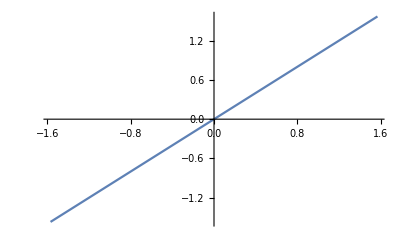

```mathematica
Plot[func[x],{x,-π/2, π/2}]
```

```mathematica
0.
θ0
```

0.

θ0

```mathematica
θ[x_, y_, θ0_,ϕ0_] := ArcSin[Sin[θ0+y]Cos[x]]
```

```mathematica
FullSimplify[D[θ[x, y, θ0, ϕ0], x]]
```

-(Sin[x] Sin[y+θ0])/(√(1-Cos[x]^2 Sin[y+θ0]^2))

```mathematica
FullSimplify[D[θ[x, y, θ0, ϕ0], y]]
```

(Cos[x] Cos[y+θ0])/(√(1-Cos[x]^2 Sin[y+θ0]^2))

```mathematica
θx[x_, y_, θ0_,ϕ0_] := -(Sin[x] Sin[y+θ0])/(√(1-Cos[x]^2 Sin[y+θ0]^2))
```

```mathematica
θ0[0.0,0.0,0.0,0.0]
```

θ0[0.,0.,0.,0.]

```mathematica
-(Sin[x] Sin[y+θ0])/(√(1-Cos[x]^2 Sin[y+θ0]^2))/.{x-> 0.0, y-> 0.0}
```

0.

```mathematica
(Cos[x] Cos[y+θ0])/(√(1-Cos[x]^2 Sin[y+θ0]^2))/.{x-> 0, y-> 0}
```

Cos[θ0]/(√(1-Sin[θ0]^2))

```mathematica
FullSimplify[D[D[θ[x, y, θ0, ϕ0], x], x]]
```

-(Cos[x] Cos[y+θ0]^2 Sin[y+θ0])/((1-Cos[x]^2 Sin[y+θ0]^2)^(3/2))

```mathematica
-(Cos[x] Cos[y+θ0]^2 Sin[y+θ0])/((1-Cos[x]^2 Sin[y+θ0]^2)^(3/2))/.{x-> 0, y-> 0}
```

```mathematica
-(Cos[θ0]^2 Sin[θ0])/((1-Sin[θ0]^2)^(3/2))
FullSimplify[-(Cos[θ0]^2 Sin[θ0])/((1-Sin[θ0]^2)^(3/2))]
```

-(Cos[θ0]^2 Sin[θ0])/((1-Sin[θ0]^2)^(3/2))

-Sin[θ0]/(√(Cos[θ0]^2))

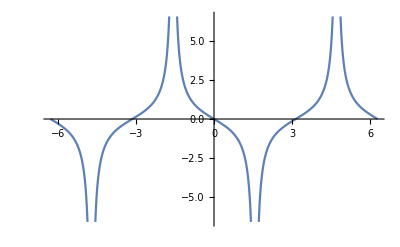

```mathematica
Plot[-(Cos[θ0]^2 Sin[θ0])/((1-Sin[θ0]^2)^(3/2)),{θ0,-2 π,2 π}]
```

```mathematica
FullSimplify[D[D[θ[x, y, θ0, ϕ0], x], y]]
```

-(Cos[y+θ0] Sin[x])/((1-Cos[x]^2 Sin[y+θ0]^2)^(3/2))

```mathematica
-(Cos[y+θ0] Sin[x])/((1-Cos[x]^2 Sin[y+θ0]^2)^(3/2))/.{x-> 0, y-> 0}
```

0

```mathematica
FullSimplify[D[D[θ[x, y, θ0, ϕ0], y], x]]
```

-(Cos[y+θ0] Sin[x])/((1-Cos[x]^2 Sin[y+θ0]^2)^(3/2))

```mathematica
FullSimplify[D[D[θ[x, y, θ0, ϕ0], y], y]]
```

-(Cos[x] Sin[x]^2 Sin[y+θ0])/((1-Cos[x]^2 Sin[y+θ0]^2)^(3/2))

```mathematica
-(Cos[x] Sin[x]^2 Sin[y+θ0])/((1-Cos[x]^2 Sin[y+θ0]^2)^(3/2))/.{x-> 0, y-> 0}
```

0

```mathematica
ϕ[x_, y_, θ0_,ϕ0_] := ϕ0 + ArcSin[Sin[x]/Cos[θ[x, y, θ0, ϕ0]]]
```

```mathematica
FullSimplify[ϕ0 + ArcSin[Sin[x]/Cos[θ[x, y, θ0, ϕ0]]]]
```

ϕ0+ArcSin[Sin[x]/(√(1-Cos[x]^2 Sin[y+θ0]^2))]

```mathematica
FullSimplify[D[ϕ[x, y, θ0, ϕ0], x]]
```

(Cos[x] Cos[y+θ0]^2)/((1-Cos[x]^2 Sin[y+θ0]^2)^(3/2) √(1+Sin[x]^2/(-1+Cos[x]^2 Sin[y+θ0]^2)))

```mathematica
(Cos[x] Cos[y+θ0]^2)/((1-Cos[x]^2 Sin[y+θ0]^2)^(3/2) √(1+Sin[x]^2/(-1+Cos[x]^2 Sin[y+θ0]^2)))/.{x-> 0, y-> 0}
```

Cos[θ0]^2/((1-Sin[θ0]^2)^(3/2))

```mathematica
FullSimplify[Cos[θ0]^2/((1-Sin[θ0]^2)^(3/2))]
```

1/(√(Cos[θ0]^2))

```mathematica
FullSimplify[D[ϕ[x, y, θ0, ϕ0], y]]
```

(Cos[x]^2 Cos[y+θ0] Sin[x] Sin[y+θ0])/((1-Cos[x]^2 Sin[y+θ0]^2)^(3/2) √(1+Sin[x]^2/(-1+Cos[x]^2 Sin[y+θ0]^2)))

```mathematica
(Cos[x]^2 Cos[y+θ0] Sin[x] Sin[y+θ0])/((1-Cos[x]^2 Sin[y+θ0]^2)^(3/2) √(1+Sin[x]^2/(-1+Cos[x]^2 Sin[y+θ0]^2)))/.{x-> 0, y-> 0}
```

0

```mathematica
FullSimplify[D[D[ϕ[x, y, θ0, ϕ0], y],y]]
```

-((-5-Cos[2 x]+2 Cos[x]^2 Cos[2 (y+θ0)]) Sin[x] √(1/(Sec[x]^2 Sec[y+θ0]^2-Tan[y+θ0]^2)))/(4 (1-Cos[x]^2 Sin[y+θ0]^2)^(3/2))

```mathematica
((-5-Cos[2 x]+2 Cos[x]^2 Cos[2 (y+θ0)]) Sin[x] √(1/(Sec[x]^2 Sec[y+θ0]^2-Tan[y+θ0]^2)))/(4 (1-Cos[x]^2 Sin[y+θ0]^2)^(3/2))/.{x-> 0, y-> 0}
```

0

```mathematica
Simplify[(Cos[θ0] (4+4 Cos[2 θ0]) Sin[θ0])/(8 (1-Sin[θ0]^2)^(5/2))]
```

Tan[θ0]/(√(Cos[θ0]^2))

```mathematica
FullSimplify[D[D[D[θ[x, y, θ0, ϕ0], y],y],y]]/.{x-> 0, y-> 0}
```

0

```mathematica
Simplify[-Cos[θ0]/((1-Sin[θ0]^2)^(3/2))]
```

-Cos[θ0]/((Cos[θ0]^2)^(3/2))

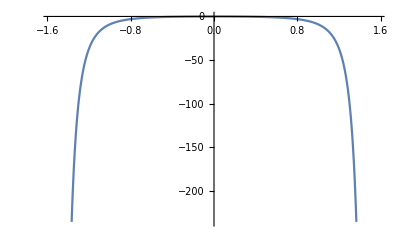

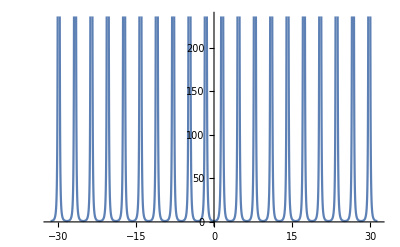

```mathematica
Plot[-(2 Tan[θ0]^2)/(√(Cos[θ0]^2)),{θ0,- π/2, π/2}]
```